## Initial setup

```mathematica
Remove["Global`*"]
```

```mathematica
e = 0.000001;
maxDepth = 3;
```

## Point sampling (current example)

```mathematica
npoints = 100;
sp = SpherePoints[npoints];
```

```mathematica
sn = sp;
```

```mathematica
Show[
Table[Graphics3D[Arrow[{sp[[i]], sp[[i]]+sn[[i]]*0.20}]],{i,npoints}],
ListPointPlot3D[sp, AspectRatio->1]
]
```

-Graphics3D-

## Octree spatial partition

```mathematica
initialWidth = Max[(Max@sp[[All,#]]&/@Range[3])-(Min@sp[[All,#]]&/@Range[3])] + 2.00 * e;
```

```mathematica
initialCenter = ((Max@sp[[All,#]]&/@Range[3])+(Min@sp[[All,#]]&/@Range[3]))/2.00;
```

```mathematica
(* { {{center}, width}, {idx1, idx2, idx3, ...} } *)
octree = {{{initialCenter, initialWidth},Table[i, {i,Length[sp]}]}};
```

```mathematica
SubdivideNode[node_, pts_]:=Module[{n, points, idx, center, width, child1, child2, child3, child4, child5, child6, child7, child8, result},
n=node;
points=pts;
idx = n[[2]];
center = n[[1]][[1]];
width = n[[1]][[2]];
(* Subdivide only if the node has more than 1 points *)
If[Length[idx]>1,
(* True: Subdivide *)
child1 = {};
child2 = {};
child3 = {};
child4 = {};
child5 = {};
child6 = {};
child7 = {};
child8 = {};
Do[
If[points[[idx[[i]]]][[1]] < center[[1]] && points[[idx[[i]]]][[2]] < center[[2]] && points[[idx[[i]]]][[3]] < center[[3]],child1 = Append[child1, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] < center[[2]] && points[[idx[[i]]]][[3]] < center[[3]],child2 = Append[child2, idx[[i]]]];
If[points[[idx[[i]]]][[1]] < center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] < center[[3]],child3 = Append[child3, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] < center[[3]],child4 = Append[child4, idx[[i]]]];
If[points[[idx[[i]]]][[1]] < center[[1]] && points[[idx[[i]]]][[2]] < center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child5 = Append[child5, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] < center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child6 = Append[child6, idx[[i]]]];
If[points[[idx[[i]]]][[1]] < center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child7 = Append[child7, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child8 = Append[child8, idx[[i]]]]
,{i,Length[idx]}];
(* Construct what to return *)
result = {};
If[Length[child1]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, -width/4.0}, width/2.0},child1}]];
If[Length[child2]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, -width/4.0}, width/2.0},child2}]];
If[Length[child3]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, -width/4.0}, width/2.0},child3}]];
If[Length[child4]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, -width/4.0}, width/2.0},child4}]];
If[Length[child5]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, +width/4.0}, width/2.0},child5}]];
If[Length[child6]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, +width/4.0}, width/2.0},child6}]];
If[Length[child7]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, +width/4.0}, width/2.0},child7}]];
If[Length[child8]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, +width/4.0}, width/2.0},child8}]];
n = result;
]; (* end if *)
n] (* end function *)
```

```mathematica
(* TODO: There's some problem here *)
SubdivideOctree[oct_, pts_]:=Module[{tr, octSub, points},
tr=oct;
points=pts;
octSub = {};
Do[
octSub = Append[octSub,SubdivideNode[tr[[i]],points]][[1]]
,{i,Length[tr]}];
octSub
]
```

```mathematica
octree
```

{{{{0.00126229,0.00790206,-5.55112×10^-17},1.98708},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}}

```mathematica
lala = SubdivideOctree[octree, sp]
```

{{{{-0.495507,-0.488867,-0.496769},0.993539},{4,7,12,15,20,25,28,33,38,41,46,49}},{{{0.498032,-0.488867,-0.496769},0.993539},{2,5,10,13,18,23,26,31,34,36,39,44,47}},{{{-0.495507,0.504671,-0.496769},0.993539},{1,6,9,14,17,19,22,27,30,35,40,43,48}},{{{0.498032,0.504671,-0.496769},0.993539},{3,8,11,16,21,24,29,32,37,42,45,50}},{{{-0.495507,-0.488867,0.496769},0.993539},{54,59,62,67,70,72,75,80,83,88,93,96}},{{{0.498032,-0.488867,0.496769},0.993539},{52,57,60,65,68,73,78,81,86,89,91,94,99}},{{{-0.495507,0.504671,0.496769},0.993539},{51,56,61,64,69,74,77,82,85,90,95,98}},{{{0.498032,0.504671,0.496769},0.993539},{53,55,58,63,66,71,76,79,84,87,92,97,100}}}

```mathematica
tr = lala;
```

```mathematica
points = sp;
```

```mathematica
octSub = {};
```

```mathematica
octSub = Append[octSub,SubdivideNode[tr[[1]],points]][[1]]
```

{{{{-0.743892,-0.737252,-0.745154},0.496769},{20}},{{{-0.247122,-0.737252,-0.745154},0.496769},{15}},{{{-0.743892,-0.240483,-0.745154},0.496769},{12,25}},{{{-0.247122,-0.240483,-0.745154},0.496769},{4,7}},{{{-0.743892,-0.737252,-0.248385},0.496769},{33,41}},{{{-0.247122,-0.737252,-0.248385},0.496769},{28,49}},{{{-0.743892,-0.240483,-0.248385},0.496769},{38,46}}}

```mathematica
tr[[6]]
```

{{{0.498032,-0.488867,0.496769},0.993539},{52,57,60,65,68,73,78,81,86,89,91,94,99}}

```mathematica
Append[octSub,SubdivideNode[tr[[5]],points]][[1]]
```

{{{{-0.743892,-0.737252,0.248385},0.496769},{54,67,75}},{{{-0.247122,-0.737252,0.248385},0.496769},{62,70}},{{{-0.743892,-0.240483,0.248385},0.496769},{59,72}},{{{-0.247122,-0.737252,0.745154},0.496769},{83}},{{{-0.743892,-0.240483,0.745154},0.496769},{80,88,93}},{{{-0.247122,-0.240483,0.745154},0.496769},{96}}}

```mathematica
octSub
```

-0.743892

```mathematica
octSub = Append[octSub,SubdivideNode[tr[[6]],points]][[1]];
```

Append::normal: Nonatomic expression expected at position 1 in Append[-0.743892,{{{{0.249647,-0.737252,0.248385},0.496769},{57,65}},{{{0.746416,-0.737252,0.248385},0.496769},{52,73}},{{{0.746416,-0.240483,0.248385},0.496769},{60,68}},{{{0.249647,-0.737252,0.745154},0.496769},{78,86,91}},{{{0.249647,-0.240483,0.745154},0.496769},{94,99}},{{{0.746416,-0.240483,0.745154},0.496769},{81,89}}}].

```mathematica
Do[
octSub = Append[octSub,SubdivideNode[tr[[i]],points]][[1]]
,{i,Length[tr]}]
```

Append::normal: Nonatomic expression expected at position 1 in Append[-0.743892,{{{{0.249647,-0.737252,0.248385},0.496769},{57,65}},{{{0.746416,-0.737252,0.248385},0.496769},{52,73}},{{{0.746416,-0.240483,0.248385},0.496769},{60,68}},{{{0.249647,-0.737252,0.745154},0.496769},{78,86,91}},{{{0.249647,-0.240483,0.745154},0.496769},{94,99}},{{{0.746416,-0.240483,0.745154},0.496769},{81,89}}}].

Append::normal: Nonatomic expression expected at position 1 in Append[-0.743892,{{{{-0.743892,0.256287,0.248385},0.496769},{51,64}},{{{-0.743892,0.753056,0.248385},0.496769},{56,69}},{{{-0.247122,0.753056,0.248385},0.496769},{61,74}},{{{-0.743892,0.256287,0.745154},0.496769},{77,85}},{{{-0.247122,0.256287,0.745154},0.496769},{90,95,98}},{{{-0.247122,0.753056,0.745154},0.496769},{82}}}].

Append::normal: Nonatomic expression expected at position 1 in Append[-0.743892,{{{{0.746416,0.256287,0.248385},0.496769},{55,63}},{{{0.249647,0.753056,0.248385},0.496769},{53,66}},{{{0.746416,0.753056,0.248385},0.496769},{58,71}},{{{0.249647,0.256287,0.745154},0.496769},{92,97,100}},{{{0.746416,0.256287,0.745154},0.496769},{76,84}},{{{0.249647,0.753056,0.745154},0.496769},{79,87}}}].

General::stop: Further output of Append::normal will be suppressed during this calculation.

## System

```mathematica
F[q_]:=If[Abs[q[[1]]]<π/2 &&Abs[q[[2]]]<π/2 && Abs[q[[3]]]<π/2 ,(2 π^(-3/2)*(1-1/2 qᵀ.q)),0.00]
```

```mathematica
Plot3D[{F[{x,y,0.00}], 2 π^(-3/2)*(Cos[x]*Cos[y]*Cos[0.00])}, {x,-π/2,π/2}, {y,-π/2, π/2}]
```

-Graphics3D-

```mathematica
F[q_]:=If[Abs[q[[1]]]<π/2 &&Abs[q[[2]]]<π/2 && Abs[q[[3]]]<π/2 ,( 2 π^(-3/2)*(Cos[q[[1]]]*Cos[q[[2]]]*Cos[q[[3]]])),0.00]
```

```mathematica
(* F[q_]:=(2π)^(-3/2)*Exp[-1/2 qᵀ.q] *)
```

```mathematica
Fo[q_,c_,w_]:=F[1/w*(q-c)]
```

```mathematica
(* Gradient field *)
```

```mathematica
V[q_]:=Sum[Fo[q, oc[i], ow] * sn[i],{i,npoints}]
```

```mathematica
VectorPlot3D[V[{x,y,z}],{x,-0.50,0.50},{y,-0.50,0.50},{z,-0.50,0.50}, VectorScaling-> Automatic]
```

-Graphics3D-

```mathematica
divV[{x_,y_,z_}]:=(V[{x+e, y, z}][[1]]-V[{x, y, z}][[1]])/e+(V[{x, y+e, z}][[2]]-V[{x, y, z}][[2]])/e+(V[{x, y, z+e}][[3]]-V[{x, y, z}][[3]])/e
```

```mathematica
Foxx[{x_,y_,z_}, c_, w_]:=(Fo[{x+e,y,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x-e,y,z},c,w])/e^2
Foyy[{x_,y_,z_}, c_, w_]:=(Fo[{x,y+e,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y-e,z},c,w])/e^2
Fozz[{x_,y_,z_}, c_, w_]:=(Fo[{x,y,z+e},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y,z-e},c,w])/e^2
```

```mathematica
(* Div[V[{x,y,z}],{x,y,z}] *)
```

```mathematica
(* v =Table[NIntegrate[Div[V[{x,y,z}],{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}],{i,npoints}] *)
```

```mathematica
v =Table[NIntegrate[divV[{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00}, Method-> "GlobalAdaptive", AccuracyGoal->50],{i,npoints}]
```

{0.332904,0.250434,0.228028,0.250434,0.333071,0.280603,0.266348,0.280603}

```mathematica
L=ParallelTable[
NIntegrate[Foxx[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Foyy[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Fozz[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00}, Method-> "GlobalAdaptive", AccuracyGoal->50],
{i,npoints},{j,npoints}]
```

{{-0.749833,-0.343148,-0.133122,-0.343148,-0.343148,-0.133122,-0.030493,-0.133122},{-0.343148,-0.749833,-0.343147,-0.133122,-0.133122,-0.343147,-0.133122,-0.0304931},{-0.133122,-0.343148,-0.749833,-0.343148,-0.030493,-0.133122,-0.343147,-0.133122},{-0.343148,-0.133122,-0.343147,-0.749833,-0.133122,-0.0304931,-0.133122,-0.343147},{-0.343148,-0.133122,-0.0304931,-0.133122,-0.749833,-0.343147,-0.133122,-0.343147},{-0.133122,-0.343148,-0.133122,-0.0304931,-0.343148,-0.749833,-0.343147,-0.133122},{-0.0304931,-0.133122,-0.343148,-0.133122,-0.133122,-0.343148,-0.749832,-0.343148},{-0.133122,-0.0304931,-0.133122,-0.343148,-0.343148,-0.133122,-0.343147,-0.749833}}

```mathematica
L = Re[L];
```

```mathematica
L//MatrixForm
```

(-0.749833 | -0.343148 | -0.133122 | -0.343148 | -0.343148 | -0.133122 | -0.030493 | -0.133122
-0.343148 | -0.749833 | -0.343147 | -0.133122 | -0.133122 | -0.343147 | -0.133122 | -0.0304931
-0.133122 | -0.343148 | -0.749833 | -0.343148 | -0.030493 | -0.133122 | -0.343147 | -0.133122
-0.343148 | -0.133122 | -0.343147 | -0.749833 | -0.133122 | -0.0304931 | -0.133122 | -0.343147
-0.343148 | -0.133122 | -0.0304931 | -0.133122 | -0.749833 | -0.343147 | -0.133122 | -0.343147
-0.133122 | -0.343148 | -0.133122 | -0.0304931 | -0.343148 | -0.749833 | -0.343147 | -0.133122
-0.0304931 | -0.133122 | -0.343148 | -0.133122 | -0.133122 | -0.343148 | -0.749832 | -0.343148
-0.133122 | -0.0304931 | -0.133122 | -0.343148 | -0.343148 | -0.133122 | -0.343147 | -0.749833)

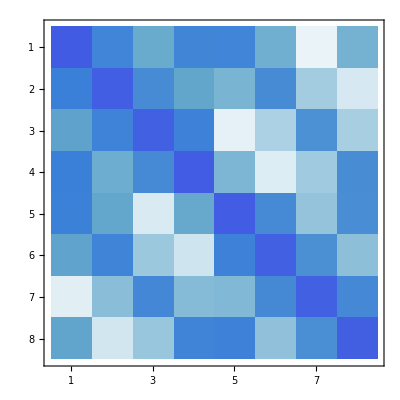

```mathematica
MatrixPlot[L]
```

```mathematica
xvec = LinearSolve[L,v]
```

{-0.26099,-0.0414596,-0.105931,-0.0414596,-0.163639,-0.12924,-0.134057,-0.12924}

```mathematica
chi[q_]:=Sum[
xvec[[i]] * Fo[q,oc[i],ow]
,{i,npoints}]
```

```mathematica
γ = Mean[Table[chi[sp[i]],{i,npoints}]];
```

```mathematica
ContourPlot3D[chi[{x,y,z}]==γ, {x, -1.50, 1.50}, {y, -1.50, 1.50},{z, -1.50, 1.50}]
```

-Graphics3D-